Fitting results:

-2.50833 va+0.860712 va^2+2.00772 vb+0.468969 va vb-0.865265 vb^2+1.51343 vg+0.179177 va vg+0.203349 vb vg-0.854146 vg^2

| Estimate | Standard Error | Confidence Interval
Aa | -2.50833 | 0.082619 | {-2.61669,-2.39997}
Ab | 2.00772 | 0.0699354 | {1.91599,2.09945}
Ag | 1.51343 | 0.0728307 | {1.41791,1.60896}
Aab | 0.468969 | 0.014676 | {0.44972,0.488218}
Aag | 0.179177 | 0.0114511 | {0.164158,0.194197}
Abg | 0.203349 | 0.0126595 | {0.186745,0.219953}
Aaa | 0.860712 | 0.0362757 | {0.813134,0.908291}
Abb | -0.865265 | 0.0291199 | {-0.903458,-0.827072}
Agg | -0.854146 | 0.034689 | {-0.899643,-0.808649}

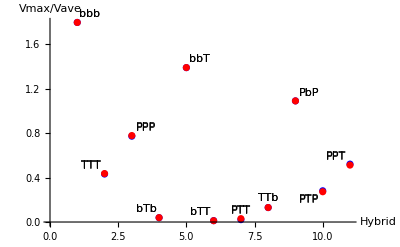

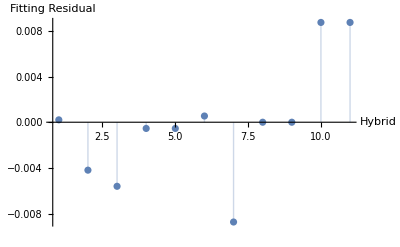

```mathematica
Vb=786.;  (* scaled vmax for bbb *)
VT=189.; (* scaled vmax for TTT *)
VP=338.; (* scaled vmax for PPP *)

Vave=(Vb+VT+VP)/3.;
Vb=Vb/Vave;
VT=VT/Vave;
VP=VP/Vave;

dtemp={{Vb,Vb,Vb,786./Vave},{VT,VT,VT,189./Vave},{VP,VP,VP,338./Vave},{Vb,VT,Vb,17./Vave},{Vb,Vb,VT,608./Vave},{Vb,VT,VT,5.4/Vave},{VP,VT,VT,9.4/Vave},{VT,VT,Vb,57./Vave},{VP,Vb,VP,477./Vave},{VP,VT,VP,123./Vave},{VP,VP,VT,228./Vave}};

dtemp1={{"bbb",786./Vave},{"TTT",189./Vave},{"PPP",338./Vave},{"bTb",17./Vave},{"bbT",608./Vave},{"bTT",5.4/Vave},{"PTT",9.4/Vave},{"TTb",57./Vave},{"PbP",477./Vave},{"PTP",123./Vave},{"PPT",228./Vave}};

dtemp2=Table[Labeled[dtemp1[[ntemp1]][[2]],dtemp1[[ntemp1]][[1]]],{ntemp1,1,Length[dtemp1]}];

Aa0=1.;  (* guess for a_alpha *)
Ab0=1.;  (* guess for a_beta *)
Ag0=1.;  (* guess for a_gamma *)
Aab0=0.01;  (* guess for a_alpha,beta *)
Aag0=0.01;   (* guess for a_alpha,gamma *)
Abg0=0.01;  (* guess for a_beta,gamma *)
Aaa0=0.01;
Abb0=0.01;
Agg0=0.01;

(* The fitting *)
ftemp=NonlinearModelFit[dtemp,Aa*va+Ab*vb+Ag*vg+Aab*va*vb+Aag*va*vg+Abg*vb*vg+Aaa*va*va+Abb*vb*vb+Agg*vg*vg,{{Aa,Aa0},{Ab,Ab0},{Ag,Ag0},{Aab,Aab0},{Aag,Aag0},{Abg,Abg0},{Aaa,Aaa0},{Abb,Abb0},{Agg,Agg0}},{va,vb,vg},Method->Automatic,MaxIterations->1000,ConfidenceLevel->0.68];

Print["Fitting results:"];
Print[ftemp["BestFit"]];
Print[ftemp["ParameterConfidenceIntervalTable"]];


(* Check fitting *)
FitEq=Normal[ftemp];
FitResult=Table[Labeled[N[FitEq/.{va->dtemp[[ntemp]][[1]],vb->dtemp[[ntemp]][[2]],vg-> dtemp[[ntemp]][[3]]}],dtemp1[[ntemp]][[1]]],{ntemp,1,Length[dtemp]}];

LinearQuadraticRatio=Table[Labeled[N[FitEq/.{va->dtemp[[ntemp]][[1]],vb->dtemp[[ntemp]][[2]],vg-> dtemp[[ntemp]][[3]]}],dtemp1[[ntemp]][[1]]],{ntemp,1,Length[dtemp]}];

Print[Show[ListPlot[dtemp2,PlotStyle->Blue],ListPlot[FitResult,PlotStyle->Red],AxesLabel->{"Hybrid","Vmax/Vave"}]];
Print[ListPlot[ftemp["FitResiduals"],Filling->Axis,AxesLabel->{"Hybrid","Fitting Residual"},PlotRange->All]];
```

```mathematica
V[3]=786./Vave;  (* scaled vmax for bbb *)
V[1]=189./Vave; (* scaled vmax for TTT *)
V[2]=338./Vave; (* scaled vmax for PPP *)

vmaxtemp=Sort[Flatten[Table[{N[Vave*FitEq/.{va->V[atemp],vb->V[btemp],vg->V[gtemp]}],atemp,btemp,gtemp}
,{atemp,1,3},{btemp,1,3},{gtemp,1,3}],2]]
```

{{-84.1979,2,1,3},{5.16201,3,1,1},{13.2206,2,1,1},{17.238,3,1,3},{57.,1,1,3},{119.179,2,1,2},{138.449,3,1,2},{168.09,2,2,3},{190.835,1,1,1},{224.179,2,2,1},{285.499,1,2,3},{287.647,3,2,1},{287.705,1,1,2},{329.712,2,3,1},{340.453,2,2,2},{341.052,3,2,3},{378.005,1,2,1},{397.888,2,3,3},{412.012,1,3,1},{431.248,3,2,2},{443.771,1,3,3},{477.,2,3,2},{485.19,1,2,2},{550.211,1,3,2},{608.238,3,3,1},{782.854,3,3,2},{785.909,3,3,3}}

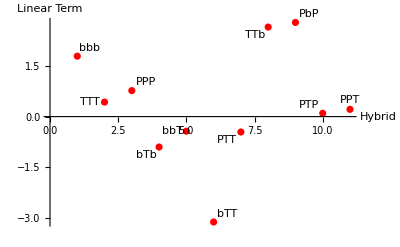

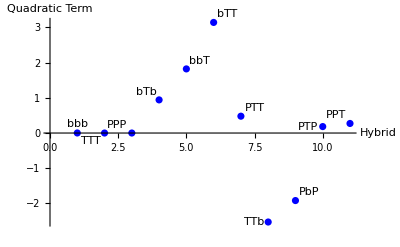

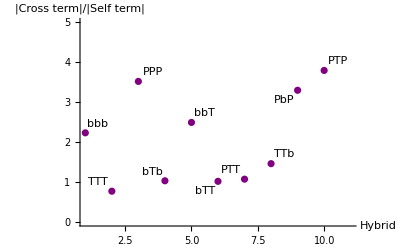

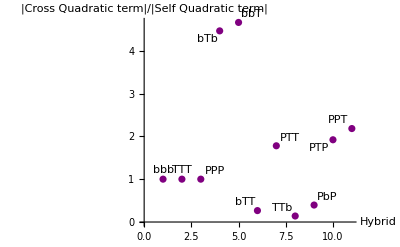

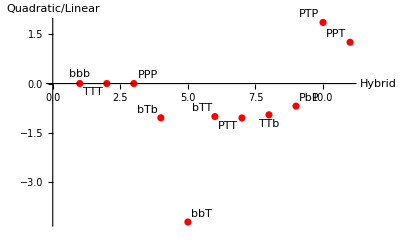

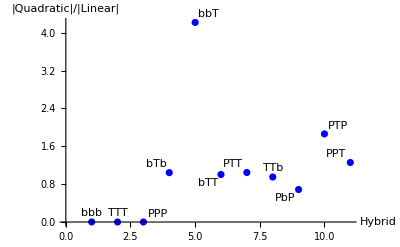

```mathematica
(* Linear terms / Quadratic terms *)
LinearTerm=Table[Labeled[N[(-2.6097471591330668 va+1.9768258559432537 vb+1.6318794651556976 vg)/.{va->dtemp[[ntemp]][[1]],vb->dtemp[[ntemp]][[2]],vg-> dtemp[[ntemp]][[3]]}],dtemp1[[ntemp]][[1]]],{ntemp,1,Length[dtemp]}];
Print[Show[ListPlot[LinearTerm,PlotStyle->Red],AxesLabel->{"Hybrid","Linear Term"}]];


QuadraticTerm=Table[Labeled[N[(0.8778003591627606 va^2+0.6274283189001735 va vb-0.9797340435213164 vb^2+0.1761087277976713 va vg+0.20441787335317524 vb vg-0.9054358599919985 vg^2)/.{va->dtemp[[ntemp]][[1]],vb->dtemp[[ntemp]][[2]],vg-> dtemp[[ntemp]][[3]]}],dtemp1[[ntemp]][[1]]],{ntemp,1,Length[dtemp]}];
Print[Show[ListPlot[QuadraticTerm,PlotStyle->Blue],AxesLabel->{"Hybrid","Quadratic Term"}]];


AbsCrossSelfRatio=Table[Labeled[N[Abs[((0.6274283189001735 va vb+0.1761087277976713 va vg+0.20441787335317524 vb vg)/(-2.6097471591330668 va+0.8778003591627606 va^2+1.9768258559432537 vb-0.9797340435213164 vb^2+1.6318794651556976 vg-0.9054358599919985 vg^2))]/.{va->dtemp[[ntemp]][[1]],vb->dtemp[[ntemp]][[2]],vg-> dtemp[[ntemp]][[3]]}],dtemp1[[ntemp]][[1]]],{ntemp,1,Length[dtemp]}];
Print[Show[ListPlot[AbsCrossSelfRatio,PlotStyle->Purple],PlotRange->{All,{0,5}},AxesLabel->{"Hybrid","|Cross term|/|Self term|"}]];

AbsCrossQSelfQRatio=Table[Labeled[N[Abs[((0.6274283189001735 va vb+0.1761087277976713 va vg+0.20441787335317524 vb vg)/(0.8778003591627606 va^2-0.9797340435213164 vb^2-0.9054358599919985 vg^2))]/.{va->dtemp[[ntemp]][[1]],vb->dtemp[[ntemp]][[2]],vg-> dtemp[[ntemp]][[3]]}],dtemp1[[ntemp]][[1]]],{ntemp,1,Length[dtemp]}];
Print[Show[ListPlot[AbsCrossQSelfQRatio,PlotStyle->Purple],AxesLabel->{"Hybrid","|Cross Quadratic term|/|Self Quadratic term|"}]];


(*
LinearQuadraticRatio=Table[Labeled[N[((-2.6097471591330668 va+1.9768258559432537 vb+1.6318794651556976 vg)/(0.8778003591627606 va^2+0.6274283189001735 va vb-0.9797340435213164 vb^2+0.1761087277976713 va vg+0.20441787335317524 vb vg-0.9054358599919985 vg^2))/.{va->dtemp[[ntemp]][[1]],vb->dtemp[[ntemp]][[2]],vg-> dtemp[[ntemp]][[3]]}],dtemp1[[ntemp]][[1]]],{ntemp,1,Length[dtemp]}];
Print[Show[ListPlot[LinearQuadraticRatio,PlotStyle->Red],AxesLabel->{"Hybrid","Linear/Quadratic"}]];
*)

QuadraticLinearRatio=Table[Labeled[N[((0.8778003591627606 va^2+0.6274283189001735 va vb-0.9797340435213164 vb^2+0.1761087277976713 va vg+0.20441787335317524 vb vg-0.9054358599919985 vg^2)/(-2.6097471591330668 va+1.9768258559432537 vb+1.6318794651556976 vg))/.{va->dtemp[[ntemp]][[1]],vb->dtemp[[ntemp]][[2]],vg-> dtemp[[ntemp]][[3]]}],dtemp1[[ntemp]][[1]]],{ntemp,1,Length[dtemp]}];
Print[Show[ListPlot[QuadraticLinearRatio,PlotStyle->Red],AxesLabel->{"Hybrid","Quadratic/Linear"}]];


AbsQuadraticLinearRatio=Table[Labeled[N[Abs[((0.8778003591627606 va^2+0.6274283189001735 va vb-0.9797340435213164 vb^2+0.1761087277976713 va vg+0.20441787335317524 vb vg-0.9054358599919985 vg^2)/(-2.6097471591330668 va+1.9768258559432537 vb+1.6318794651556976 vg))]/.{va->dtemp[[ntemp]][[1]],vb->dtemp[[ntemp]][[2]],vg-> dtemp[[ntemp]][[3]]}],dtemp1[[ntemp]][[1]]],{ntemp,1,Length[dtemp]}];
Print[Show[ListPlot[AbsQuadraticLinearRatio,PlotStyle->Blue],AxesLabel->{"Hybrid","|Quadratic|/|Linear|"}]];

(*
QuadraticFraction=Table[Labeled[N[((0.8778003591627606 va^2+0.6274283189001735 va vb-0.9797340435213164 vb^2+0.1761087277976713 va vg+0.20441787335317524 vb vg-0.9054358599919985 vg^2)/FitEq)/.{va->dtemp[[ntemp]][[1]],vb->dtemp[[ntemp]][[2]],vg-> dtemp[[ntemp]][[3]]}],dtemp1[[ntemp]][[1]]],{ntemp,1,Length[dtemp]}];
Print[Show[ListPlot[QuadraticFraction,PlotStyle->Blue],AxesLabel->{"Hybrid","Quadratic Fraction"}]];
*)
```

```mathematica
Print["Vb = ",Vb,"  VP = ",VP,"  VT = ",VT];
```

Vb = 1.79589  VP = 0.772277  VT = 0.431835

```mathematica
QuadraticLinearRatio
```

{0.00105237bbb,0.00025305TTT,0.000452544PPP,-1.04299bTb,-4.21596bbT,-1.00396bTT,-1.04594PTT,-0.95099TTb,-0.686086PbP,1.86098PTP,1.25731PPT}